### Explicit Examples

```mathematica
α = ({{α1}, {α2}, {α3}, {α4}});
β1=({{β11}, {β12}, {β13}, {β14}});
β2=({{β21}, {β22}, {β23}, {β24}});
β3=({{β31}, {β32}, {β33}, {β34}});
β4=({{β41}, {β42}, {β43}, {β44}});
A0=({{0, 0, 0, 0}, {A021, 0, 0, 0}, {A031, A032, 0, 0}, {A041, A042, A043, 0}}); (* A0=({{A011, A012, A013, A014}, {A021, A022, A023, A024}, {A031, A032, A033, A034}, {A041, A042, A043, A044}}); *)
A1=({{0, 0, 0, 0}, {A121, 0, 0, 0}, {A131, A132, 0, 0}, {A141, A142, A143, 0}}); (* Subscript[A, 1]=({{A111, A112, A113, A114}, {A121, A122, A123, A124}, {A131, A132, A113, A134}, {A141, A142, A143, A144}}); *)
B0=({{0, 0, 0, 0}, {B021, 0, 0, 0}, {B031, B032, 0, 0}, {B041, B042, B043, 0}}); (* Subscript[B, 0]=({{B011, B012, B013, B014}, {B021, B022, B023, B024}, {B031, B032, B033, B034}, {B041, B042, B043, B044}}); *)
B1=({{0, 0, 0, 0}, {B121, 0, 0, 0}, {B131, B132, 0, 0}, {B141, B142, B143, 0}}); (* Subscript[B, 1]=({{B111, B112, B113, B114}, {B121, B122, B123, B124}, {B131, B132, B133, B134}, {B141, B142, B143, B144}}); *)
e = ({{1}, {1}, {1}, {1}});
higherConstraints[A011_,A012_,A013_,A014_,A021_,A022_,A023_,A024_,A031_,A032_,A033_,A034_,A041_,A042_,A043_,A044_,
A111_,A112_,A113_,A114_,A121_,A122_,A123_,A124_,A131_,A132_,A133_,A134_,A141_,A142_,A143_,A144_,
B011_,B012_,B013_,B014_,B021_,B022_,B023_,B024_,B031_,B032_,B033_,B034_,B041_,B042_,B043_,B044_,
B111_,B112_,B113_,B114_,B121_,B122_,B123_,B124_,B131_,B132_,B133_,B134_,B141_,B142_,B143_,B144_,
α1_,α2_,α3_,α4_,β11_,β12_,β13_,β14_,β21_,β22_,β23_,β24_,β31_,β32_,β33_,β34_,β41_,β42_,β43_,β44_] := {α1+α2+α3+α4==1,β11+β12+β13+β14==1,β21+β22+β23+β24==0,β31+β32+β33+β34==0,β41+β42+β43+β44==0,B121 β12+B131 β13+B132 β13+B141 β14+B142 β14+B143 β14==0,B121 β22+B131 β23+B132 β23+B141 β24+B142 β24+B143 β24==1,B121 β32+B131 β33+B132 β33+B141 β34+B142 β34+B143 β34==0,B121 β42+B131 β43+B132 β43+B141 β44+B142 β44+B143 β44==0,A021 α2+A031 α3+A032 α3+A041 α4+A042 α4+A043 α4==1/2,B021 α2+B031 α3+B032 α3+B041 α4+B042 α4+B043 α4==1,B021^2 α2+(B031+B032)^2 α3+(B041+B042+B043)^2 α4==3/2,A121 β12+A131 β13+A132 β13+A141 β14+A142 β14+A143 β14==1,A121 β22+A131 β23+A132 β23+A141 β24+A142 β24+A143 β24==0,A121 β32+A131 β33+A132 β33+A141 β34+A142 β34+A143 β34==-1,A121 β42+A131 β43+A132 β43+A141 β44+A142 β44+A143 β44==0,B121^2 β12+(B131+B132)^2 β13+(B141+B142+B143)^2 β14==1,B121^2 β22+(B131+B132)^2 β23+(B141+B142+B143)^2 β24==0,B121^2 β32+(B131+B132)^2 β33+(B141+B142+B143)^2 β34==-1,B121^2 β42+(B131+B132)^2 β43+(B141+B142+B143)^2 β44==2,B121 B132 β13+(B121 B142+(B131+B132) B143) β14==0,B121 B132 β23+(B121 B142+(B131+B132) B143) β24==0,B121 B132 β33+(B121 B142+(B131+B132) B143) β34==0,B121 B132 β43+(B121 B142+(B131+B132) B143) β44==1,1/2 (A132 B021 β13+(A142 B021+A143 (B031+B032)) β14)+1/3 (A132 B021 β33+(A142 B021+A143 (B031+B032)) β34)==0}
zmin = -14;
zmax = 1;
wmin = -3;
wmax = 3;
ymin = -4;
ymax = 4;
```

### SRI1W1

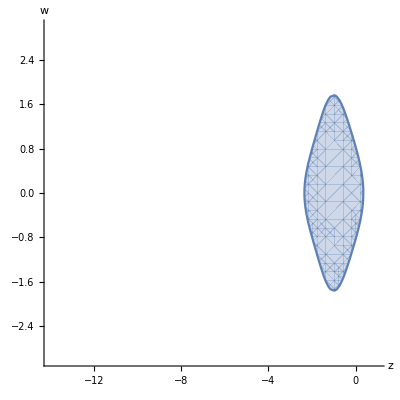

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
Get["stableRegionsEq.mx"]
Set[Evaluate[Flatten[Transpose[({{A011, A012, A013, A014}, {A021, A022, A023, A024}, {A031, A032, A033, A034}, {A041, A042, A043, A044}})]]], Flatten[Transpose[({{0, 0, 0, 0}, {3/4, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}})]] ];
Set[Evaluate[Flatten[Transpose[({{A111, A112, A113, A114}, {A121, A122, A123, A124}, {A131, A132, A133, A134}, {A141, A142, A143, A144}})]]], Flatten[Transpose[({{0, 0, 0, 0}, {1/4, 0, 0, 0}, {1, 0, 0, 0}, {0, 0, 1/4, 0}})]] ];
Set[Evaluate[Flatten[Transpose[({{B011, B012, B013, B014}, {B021, B022, B023, B024}, {B031, B032, B033, B034}, {B041, B042, B043, B044}})]]], Flatten[Transpose[({{0, 0, 0, 0}, {3/2, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}})]] ];
Set[Evaluate[Flatten[Transpose[({{B111, B112, B113, B114}, {B121, B122, B123, B124}, {B131, B132, B133, B134}, {B141, B142, B143, B144}})]]], Flatten[Transpose[({{0, 0, 0, 0}, {1/2, 0, 0, 0}, {-1, 0, 0, 0}, {-5, 3, 1/2, 0}})]] ];
Set[Evaluate[Flatten[Transpose[({{α1}, {α2}, {α3}, {α4}})]]], Flatten[Transpose[({{1/3}, {2/3}, {0}, {0}})] ]];
Set[Evaluate[Flatten[Transpose[({{β11}, {β12}, {β13}, {β14}})]]], Flatten[Transpose[({{-1}, {4/3}, {2/3}, {0}})] ]];
Set[Evaluate[Flatten[Transpose[({{β21}, {β22}, {β23}, {β24}})]]], Flatten[Transpose[({{-1}, {4/3}, {-1/3}, {0}})] ]];
Set[Evaluate[Flatten[Transpose[({{β31}, {β32}, {β33}, {β34}})]]], Flatten[Transpose[({{2}, {-4/3}, {-2/3}, {0}})] ]];
Set[Evaluate[Flatten[Transpose[({{β41}, {β42}, {β43}, {β44}})]]], Flatten[Transpose[({{-2}, {5/3}, {-2/3}, {1}})] ]];
stableRegions = Simplify[stableRegionsEq];
RegionPlot[Abs[stableRegions]<1,{z,zmin,zmax},{w,wmin,wmax},AxesLabel->Automatic,Axes->True,Frame->None]
```

### SRI2W1

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

7.72052

-Graphics3D-

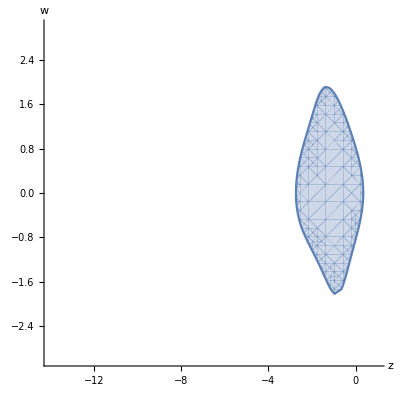

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
Get["stableRegionsEq.mx"]
Set[Evaluate[Flatten[Transpose[({{A011, A012, A013, A014}, {A021, A022, A023, A024}, {A031, A032, A033, A034}, {A041, A042, A043, A044}})]]], Flatten[Transpose[({{0, 0, 0, 0}, {1, 0, 0, 0}, {1/4, 1/4, 0, 0}, {0, 0, 0, 0}})]] ];
Set[Evaluate[Flatten[Transpose[({{A111, A112, A113, A114}, {A121, A122, A123, A124}, {A131, A132, A133, A134}, {A141, A142, A143, A144}})]]], Flatten[Transpose[({{0, 0, 0, 0}, {1/4, 0, 0, 0}, {1, 0, 0, 0}, {0, 0, 1/4, 0}})]] ];
Set[Evaluate[Flatten[Transpose[({{B011, B012, B013, B014}, {B021, B022, B023, B024}, {B031, B032, B033, B034}, {B041, B042, B043, B044}})]]], Flatten[Transpose[({{0, 0, 0, 0}, {0, 0, 0, 0}, {1, 1/2, 0, 0}, {0, 0, 0, 0}})]] ];
Set[Evaluate[Flatten[Transpose[({{B111, B112, B113, B114}, {B121, B122, B123, B124}, {B131, B132, B133, B134}, {B141, B142, B143, B144}})]]], Flatten[Transpose[({{0, 0, 0, 0}, {-1/2, 0, 0, 0}, {1, 0, 0, 0}, {2, -1, 1/2, 0}})]] ];
Set[Evaluate[Flatten[Transpose[({{α1}, {α2}, {α3}, {α4}})]]], Flatten[Transpose[({{1/6}, {1/6}, {2/3}, {0}})] ]];
Set[Evaluate[Flatten[Transpose[({{β11}, {β12}, {β13}, {β14}})]]], Flatten[Transpose[({{-1}, {4/3}, {2/3}, {0}})] ]];
Set[Evaluate[Flatten[Transpose[({{β21}, {β22}, {β23}, {β24}})]]], Flatten[Transpose[({{1}, {-4/3}, {1/3}, {0}})] ]];
Set[Evaluate[Flatten[Transpose[({{β31}, {β32}, {β33}, {β34}})]]], Flatten[Transpose[({{2}, {-4/3}, {-2/3}, {0}})] ]];
Set[Evaluate[Flatten[Transpose[({{β41}, {β42}, {β43}, {β44}})]]], Flatten[Transpose[({{-2}, {5/3}, {-2/3}, {1}})] ]];

higherConstraints[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq];
Re[NIntegrate[Boole[Abs[stableRegions]<1],{z,zmin,zmax},{w,wmin,wmax},Method->{"AdaptiveMonteCarlo"}]]
RegionPlot3D[Abs[stableRegions /. {z-> x + ⅈ y}]<1,{x,zmin,zmax},{y,ymin,ymax},{w,wmin,wmax},AxesLabel->Automatic]
RegionPlot[Abs[stableRegions]<1,{z,zmin,zmax},{w,wmin,wmax},AxesLabel->Automatic,Axes->True,Frame->None]
```

### Euler Maruyama

w^2+Abs[1+z]^2

3.1179

-Graphics3D-

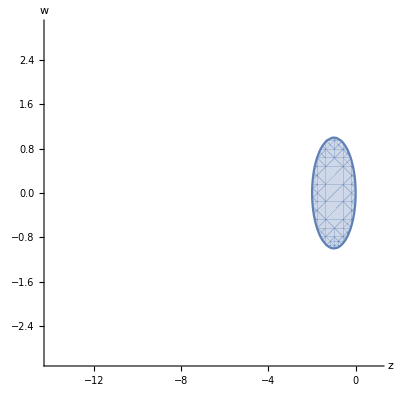

```mathematica
stableRegions = Abs[1+z]^2 + w^2
Re[NIntegrate[Boole[Abs[stableRegions]<1],{z,zmin,zmax},{w,wmin,wmax},Method->{"AdaptiveMonteCarlo"}]]
RegionPlot3D[Abs[stableRegions /. {z-> x + ⅈ y}]<1,{x,zmin,zmax},{y,ymin,ymax},{w,wmin,wmax},AxesLabel->Automatic]
RegionPlot[Abs[stableRegions]<1,{z,zmin,zmax},{w,wmin,wmax},AxesLabel->Automatic,Axes->True,Frame->None]
```

$Aborted

2.37641×10^-6 w^8+w^7 (0.0000538729-0.0000232852 z)+w^6 (-0.000309149+0.000710872 z+0.00340233 z^2)+w^5 (-0.00553542+0.00239527 z-0.00625711 z^2-0.00200828 z^3)+w^4 (0.156816-0.113985 z-0.0982832 z^2-0.00920224 z^3+0.0000906389 z^4)+w^3 (0.00477081+0.0995738 z+0.103972 z^2+0.0455873 z^3+0.00454599 z^4+0.0000839181 z^5)+w^2 (1.33333+2.35685 z+1.40641 z^2+0.261043 z^3+0.0210521 z^4+0.000603781 z^5+7.98252×10^-6 z^6)+z (2.+2. z+1.17333 z^2+0.432595 z^3+0.0959274 z^4+0.0121413 z^5+0.000802558 z^6+0.000021438 z^7)

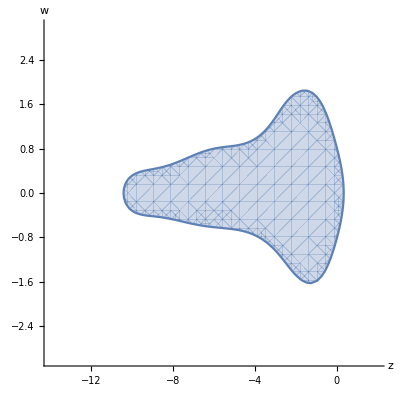

2.37641×10^-6 w^8+w^7 (0.0000538729-0.0000232852 z)+w^6 (-0.000309149+0.000710872 z+0.00340233 z^2)+w^5 (-0.00553542+0.00239527 z-0.00625711 z^2-0.00200828 z^3)+w^4 (0.156816-0.113985 z-0.0982832 z^2-0.00920224 z^3+0.0000906389 z^4)+w^3 (0.00477081+0.0995738 z+0.103972 z^2+0.0455873 z^3+0.00454599 z^4+0.0000839181 z^5)+w^2 (1.33333+2.35685 z+1.40641 z^2+0.261043 z^3+0.0210521 z^4+0.000603781 z^5+7.98252×10^-6 z^6)+z (2.+2. z+1.17333 z^2+0.432595 z^3+0.0959274 z^4+0.0121413 z^5+0.000802558 z^6+0.000021438 z^7)

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq];
SRIOpt2Region = FullSimplify[stableRegions /. {A021-> 0.13803991182809405,A031->0.5764629771061757,A032->  0.4235370228938241,A041-> 0.45988142444172125,A042->  0.8084859191118128,A043-> -0.2683673489095204,A121 ->  0.45482884244918836,A131->  0.7519704601202507, A132-> 0.24802953987974916,A141->  0.6961685917464052, A142->0.3460790565637937, A143->  -0.04224764831019894,B021-> 0.08513289389320751, B031-> 1.0272930820405226, B032->0.4565894293733811, B041-> 1.7266402546369712,B042->  -0.46040416640520754, B043-> -0.9623742513556953, B121-> 0.6744100174205603, B131-> -0.07377591084107533,B132-> -0.4985455217486592,B141-> -0.5623853411970345,B142-> 0.023606441329882558,B143-> -0.8953332413687689,α1-> -0.14925077940925455,α2-> 0.7532260416025327,α3-> 0.6911225838401098,α4-> -0.2950978480741201,β11-> -0.4550650633914512,β12->0.8347196075716,β13-> 0.3790963153683881,β14-> 0.24124914164997122,β21-> -0.5014671170389827,β22-> 0.9198342527636846,β23-> -0.2556662881012024,β24-> -0.16270085567402398,β31-> 1.4550650304633204,β32-> -0.8347196116875014,β33-> -0.37909625532888075,β34 -> -0.24124916721822443,β41-> -0.4998591615011572,β42-> 0.9168848205568053,β43-> -1.4115003346202473,β44 -> 0.994474673400943}]
RegionPlot[Abs[SRIOpt2Region]<1,{z,zmin,2},{w,-3,3},AxesLabel->Automatic,Axes->True,Frame->None]
```

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]

Set[{A021,A031,A032,A041,A042,A043,A121,A131,A132,A141,A142,A143,B021,B031,B032,B041,B042,B043,B121,B131,B132,B141,B142,B143,α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44},{0.13803991182809405,0.5764629771061757,0.4235370228938241,0.45988142444172125,0.8084859191118128,-0.2683673489095204,0.45482884244918836,0.7519704601202507,0.24802953987974916,0.6961685917464052,0.3460790565637937,-0.04224764831019894,0.08513289389320751,1.0272930820405226,0.4565894293733811,1.7266402546369712,-0.46040416640520754,-0.9623742513556953,0.6744100174205603,-0.07377591084107533,-0.4985455217486592,-0.5623853411970345,0.023606441329882558,-0.8953332413687689,-0.14925077940925455,0.7532260416025327,0.6911225838401098,-0.2950978480741201,-0.4550650633914512,0.8347196075716,0.3790963153683881,0.24124914164997122,-0.5014671170389827,0.9198342527636846,-0.2556662881012024,-0.16270085567402398,1.4550650304633204,-0.8347196116875014,-0.37909625532888075,-0.24124916721822443,-0.4998591615011572,0.9168848205568053,-1.4115003346202473,0.994474673400943}]
higherConstraints[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq]
```

{0.13804,0.576463,0.423537,0.459881,0.808486,-0.268367,0.454829,0.75197,0.24803,0.696169,0.346079,-0.0422476,0.0851329,1.02729,0.456589,1.72664,-0.460404,-0.962374,0.67441,-0.0737759,-0.498546,-0.562385,0.0236064,-0.895333,-0.149251,0.753226,0.691123,-0.295098,-0.455065,0.83472,0.379096,0.241249,-0.501467,0.919834,-0.255666,-0.162701,1.45507,-0.83472,-0.379096,-0.241249,-0.499859,0.916885,-1.4115,0.994475}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

2.37641×10^-6 w^8+w^7 (0.0000538729-0.0000232852 z)+w^6 (-0.000309149+0.000710872 z+0.00340233 z^2)+w^5 (-0.00553542+0.00239527 z-0.00625711 z^2-0.00200828 z^3)+w^4 (0.156816-0.113985 z-0.0982832 z^2-0.00920224 z^3+0.0000906389 z^4)+w^3 (0.00477081+0.0995738 z+0.103972 z^2+0.0455873 z^3+0.00454599 z^4+0.0000839181 z^5)+w^2 (1.33333+2.35685 z+1.40641 z^2+0.261043 z^3+0.0210521 z^4+0.000603781 z^5+7.98252×10^-6 z^6)+z (2.+2. z+1.17333 z^2+0.432595 z^3+0.0959274 z^4+0.0121413 z^5+0.000802558 z^6+0.000021438 z^7)

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq];
SRIOpt2Region = Simplify[stableRegions /. {A021-> 0.13803991182809405,A031->0.5764629771061757,A032->  0.4235370228938241,A041-> 0.45988142444172125,A042->  0.8084859191118128,A043-> -0.2683673489095204,A121 ->  0.45482884244918836,A131->  0.7519704601202507, A132-> 0.24802953987974916,A141->  0.6961685917464052, A142->0.3460790565637937, A143->  -0.04224764831019894,B021-> 0.08513289389320751, B031-> 1.0272930820405226, B032->0.4565894293733811, B041-> 1.7266402546369712,B042->  -0.46040416640520754, B043-> -0.9623742513556953, B121-> 0.6744100174205603, B131-> -0.07377591084107533,B132-> -0.4985455217486592,B141-> -0.5623853411970345,B142-> 0.023606441329882558,B143-> -0.8953332413687689,α1-> -0.14925077940925455,α2-> 0.7532260416025327,α3-> 0.6911225838401098,α4-> -0.2950978480741201,β11-> -0.4550650633914512,β12->0.8347196075716,β13-> 0.3790963153683881,β14-> 0.24124914164997122,β21-> -0.5014671170389827,β22-> 0.9198342527636846,β23-> -0.2556662881012024,β24-> -0.16270085567402398,β31-> 1.4550650304633204,β32-> -0.8347196116875014,β33-> -0.37909625532888075,β34 -> -0.24124916721822443,β41-> -0.4998591615011572,β42-> 0.9168848205568053,β43-> -1.4115003346202473,β44 -> 0.994474673400943}]
```